```mathematica
<<Units`
<<PhysicalConstants`
```

General::obspkg: PhysicalConstants` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
fSpace[min_,max_,steps_,f_: Log]:=InverseFunction[f]/@Range[f@min,f@max,(f@max-f@min)/(steps-1)]
```

#### Import data thief of WD mass-density + WD mass-radius relations

```mathematica
WD=Import["/Users/NewUser/Documents/Qballs/WD.csv"];
WDrad=Import["/Users/NewUser/Documents/Qballs/WDradius.csv"];
Massreverse=Interpolation[Reverse/@WD];
WDplot=Interpolation[WD];Radplot=Interpolation[WDrad];
```

```mathematica
Convert[Radplot[1.25]SolarRadius,Kilo Meter]
```

3328.47 Kilo Meter

```mathematica
Convert[Radplot[0.85]SolarRadius,Kilo Meter]
```

6392.93 Kilo Meter

#### V_esc

```mathematica
Clear[vesc]
vesc[M_]:=Convert[Sqrt[2GravitationalConstant*M/Radplot[M]*SolarMass/SolarRadius] 1/SpeedOfLight,d]
```

```mathematica
vesc[1.25]
```

0.0333087

```mathematica
vesc[0.85]
```

0.0198191

#### λ_T as function of mass

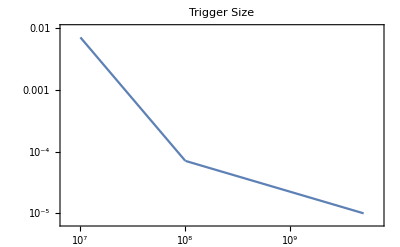

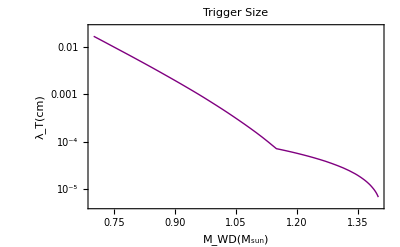

```mathematica
trigger[ρ_]:=Piecewise[{{10^-5*(ρ/(5*10^9))^(-1/2),ρ>10^8},{1/(10000 √2)*(ρ/10^8)^-2,ρ<=10^8}}]
triggermass=Interpolation[Table[{WDplot[ρ],trigger[ρ]},{ρ,fSpace[10^6,5*10^9,1000]}]];
LogLogPlot[{trigger[ρ]},{ρ,5*10^9,10^7},PlotLabel->"Trigger Size",Frame->True]
LogPlot[triggermass[M],{M,0.7,1.4},PlotLabel->"Trigger Size",Frame->True,PlotStyle->{Thick,Purple},FrameLabel->{"M_WD(M_sun)","λ_T(cm)"},FrameStyle->Black]
```

#### E_boom (in GeV) as function of WD mass

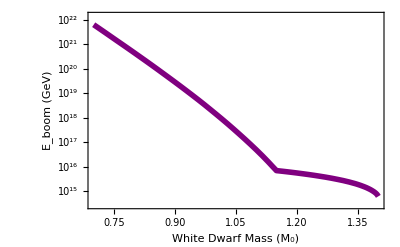

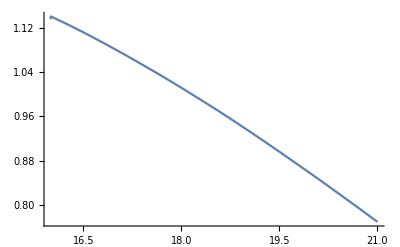

```mathematica
eboom[M_]:=Convert[(Massreverse[M]*Gram/Centimeter^3 SpeedOfLight^2)/(12 Giga ElectronVolt)*4 Pi/3(triggermass[M]Centimeter)^3*(Mega ElectronVolt)1/(Giga ElectronVolt),d]
eboomreverse[mdm_]:=Interpolation[Table[{Log10[eboom[M]],M},{M,0.7,1.37,0.01}]][mdm]
LogPlot[eboom[M],{M,0.7,1.4},FrameLabel->{"White Dwarf Mass (M_0)","E_boom (GeV)"},Frame->True,FrameStyle->Black,PlotStyle-> {Purple,Thickness[0.01]}, LabelStyle-> Directive[Bold]]
Plot[eboomreverse[logmdm],{logmdm,16,21}]
```

```mathematica
eboom[1.25]
```

4.23537×10^15

```mathematica
eboom[0.85]
```

1.14774×10^20

#### Model-dependent crust stopping calculation (R_c~ km, ρ_c~ ρ_interior)

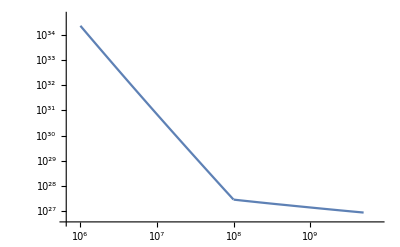

```mathematica
LogLogPlot[Convert[((Mega ElectronVolt)/vesc[WDplot[ρ]]^2(trigger[ρ]*Centimeter)^2*ρ Gram/Centimeter^3*1/(12 Giga ElectronVolt)*SpeedOfLight^2(1Kilo Meter))1/(Giga ElectronVolt),d],{ρ,10^6,5*10^9}]
```

#### Diffusion time (for trigger size) scales as 1/ρ by definition. Diffusion vs. transit comparision

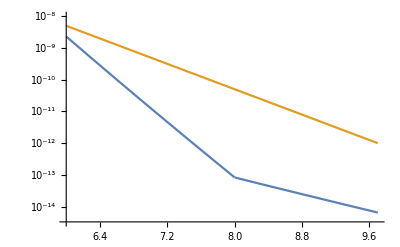

```mathematica
LogPlot[{Convert[(trigger[10^ρ]Centimeter)/(vesc[WDplot[10^ρ]]SpeedOfLight),Second] 1/Second,10^-12((5*10^9)/10^ρ)},{ρ,Log10[10^6],Log10[5*10^9]}]
```

```mathematica
snrate=0.3/Century; 
whitedwarfdistribution[m_] := 1/(0.14 Sqrt[2 π])Exp[(-(m - 0.64)^2)/(2 (0.14)^2)];
Qfunction = (FullSimplify[Re[Integrate[whitedwarfdistribution[m], {m,x, ∞}]]]);
Q=Qfunction/.{x->(If[eboomreverse[logmdm]≥ 0.85, eboomreverse[logmdm], 0.85])};
```

#### Transit Constraints

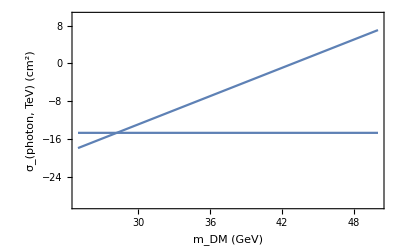

```mathematica
crust=Log10[Convert[vesc[1.25]^2/(10^32 Centimeter^-3*1 Kilo Meter)10^mdm/ϵ,Centimeter^2] 1/Centimeter^2];
transitboom=Log10[10^-3/ϵ*triggermass[1.25]^2];
crustplot=Plot[crust/.ϵ->10^3,{mdm,25,50}];
photontransit=Plot[transitboom/.ϵ->10^3,{mdm,25,50}];
fluxlimit=Plot[( 100 Sign[x-48]),{x,24,50},ExclusionsStyle->Red,PlotRange->{-30,10}];
canvastransit=Plot[-100,{x,25,50},Frame->True,FrameStyle->Black,FrameLabel->{"m_DM (GeV)", "σ_(photon, TeV) (cm^2)"},PlotRange->{-30,10},Axes->None];
Show[canvastransit,crustplot,photontransit]
```

#### Collision Constraints

```mathematica
σcollision=Γcollision ((ρdm/mdm)^2 (vesc/v)^3 v 4 Pi/3 Rwd^3)^-1;
σobsRX=Convert[σcollision/.{Γcollision->1/(5Giga Year),Rwd->Radplot[1.25]SolarRadius,vesc->vesc[1.25]SpeedOfLight,mdm->10^logmdm Giga ElectronVolt,v->10^-3 SpeedOfLight,ρdm->0.4 (Giga ElectronVolt)/Centimeter^3},Centimeter^2] 1/Centimeter^2;
σobsNuStar=Convert[σcollision/.{Γcollision->1/(5Giga Year),Rwd->Radplot[1.25]SolarRadius,vesc->vesc[1.25]SpeedOfLight,mdm->10^logmdm Giga ElectronVolt,v->10^-3 SpeedOfLight,ρdm->10^3 (Giga ElectronVolt)/Centimeter^3},Centimeter^2] 1/Centimeter^2;
```

```mathematica
σobsRX/.logmdm->Log10[eboom[1.25]]
```

4.155

```mathematica
σobsNuStar/.logmdm->Log10[eboom[1.25]]
```

6.648×10^-7

```mathematica
σfun=Convert[σcollision*1/Century/.{Rwd->Radplot[1.25]SolarRadius,vesc->vesc[1.25]SpeedOfLight,mdm->10^logmdm Giga ElectronVolt,v->10^-3 SpeedOfLight,ρdm->0.4 (Giga ElectronVolt)/Centimeter^3},Centimeter^2] 1/Centimeter^2;
```

```mathematica
σSN=σfun/.{Γcollision->snrate*Century*1/(10^10 Q)};
```

```mathematica
canvascollision=Plot[-100,{logmdm,15,21},Frame->True,FrameStyle->Black,FrameLabel->{"m_DM (GeV)", "σ_(DM - DM) (cm^2)"},PlotRange->{-35,-10},Axes->None];
```

```mathematica
SNcollision=Plot[Log10[σSN],{logmdm,16,21},PlotStyle->{Green,Thick}];
```

```mathematica
RXcollision=Plot[Log10[σobsRX],{logmdm,15,21},PlotStyle->{Blue,Thick}];
NuStarcollision=Plot[Log10[σobsNuStar],{logmdm,15,21},PlotStyle->{Gray,Thick}];
```

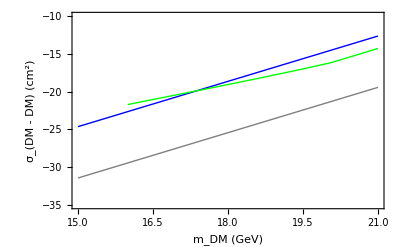

```mathematica
Show[canvascollision,RXcollision,NuStarcollision,SNcollision]
```

#### Decay Constraints

```mathematica
τdm=1/Γdecay(ρdm/mdm) (vesc/v)4 Pi/3 Rwd^3;
```

```mathematica
τobsRX=Convert[τdm/.{Γdecay->1/(5Giga Year),Rwd->Radplot[1.25]SolarRadius,vesc->vesc[1.25]SpeedOfLight,mdm->10^logmdm Giga ElectronVolt,v->10^-3 SpeedOfLight,ρdm->0.4 (Giga ElectronVolt)/Centimeter^3},Giga Year] 1/(Giga Year);
τobsNuStar=Convert[τdm/.{Γdecay->1/(5Giga Year),Rwd->Radplot[1.25]SolarRadius,vesc->vesc[1.25]SpeedOfLight,mdm->10^logmdm Giga ElectronVolt,v->10^-3 SpeedOfLight,ρdm->10^3 (Giga ElectronVolt)/Centimeter^3},Giga Year] 1/(Giga Year);
```

```mathematica
τobsRX/.logmdm->Log10[eboom[1.25]]
```

2.42951×10^12

```mathematica
τobsNuStar/.logmdm->Log10[eboom[1.25]]
```

6.07378×10^15

```mathematica
τfun=Convert[τdm*Century/.{Rwd->Radplot[1.25]SolarRadius,vesc->vesc[1.25]SpeedOfLight,mdm->10^logmdm Giga ElectronVolt,v->10^-3 SpeedOfLight,ρdm->0.4 (Giga ElectronVolt)/Centimeter^3},Giga Year] 1/(Giga Year);
```

```mathematica
τSN=τfun/.{Γdecay->snrate*Century*1/(10^10 Q)};
```

```mathematica
SNdecay=Plot[Log10[τSN],{logmdm,16,21},PlotStyle->{Green,Thick}];
```

```mathematica
RXdecay=Plot[Log10[τobsRX],{logmdm,15,21},PlotStyle->{Blue,Thick}];
NuStardecay=Plot[Log10[τobsNuStar],{logmdm,15,21},PlotStyle->{Gray,Thick}];
```

```mathematica
canvasdecay=Plot[-100,{logmdm,15,21},Frame->True,FrameStyle->Black,FrameLabel->{"m_DM (GeV)", "τ_DM (Gyr)"},PlotRange->{5,18},Axes->None];
```

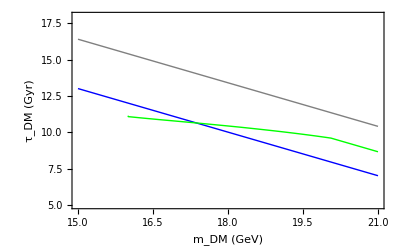

```mathematica
Show[canvasdecay,RXdecay,NuStardecay,SNdecay]
```

#### Q-ball boom

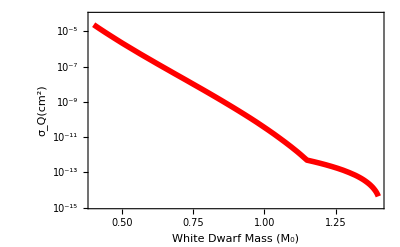

```mathematica
LogPlot[1/10^4*(triggermass[M])^2,{M,0.4,1.4},Frame->True,FrameLabel->{"White Dwarf Mass (M_0)","σ_Q(cm^2)"},FrameStyle->Black,PlotStyle-> {Red,Thickness[0.01]}, LabelStyle-> Directive[Bold]]
```